2000000000000/(s (2000010+s)+20000000 (1+100000 β))

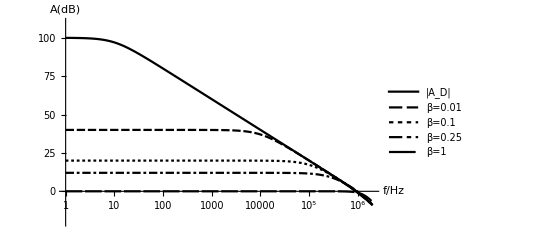

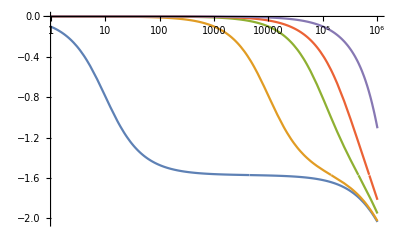

```mathematica
AD[s_]:=AD0/(1+s/ωC1)×1/(1+s/ωC2);
ACL[s_,β_]:=AD[s]/(1+AD[s] β);
FullSimplify[ACL[s,β]]
AD0=10^5;ωC1=10;ωC2=20×10^5;
LogLinearPlot[{
20*Log10[Abs[ACL[ⅈ ω,0]]],
20*Log10[Abs[ACL[ⅈ ω,0.01]]],
20*Log10[Abs[ACL[ⅈ ω,0.1]]],
20*Log10[Abs[ACL[ⅈ ω,0.25]]],
20*Log10[Abs[ACL[ⅈ ω,1]]]},{ω,1,2000000},PlotLegends->{"|A_D|","β=0.01","β=0.1","β=0.25","β=1"},PlotTheme->"Monochrome",PlotRange->{-20,110},AxesLabel->{"f/Hz","A(dB)"}]
LogLinearPlot[{
Arg[ACL[ⅈ ω,0]],
Arg[ACL[ⅈ ω,0.01]],
Arg[ACL[ⅈ ω,0.1]],
Arg[ACL[ⅈ ω,0.25]],
Arg[ACL[ⅈ ω,1]]},{ω,1,1000000}]
```

```mathematica
ooo=FindRoot[20*Log10[Abs[ACL[ⅈ ω,0]]]==100-.2,{ω,0.1}]
1/(ω/.ooo)
```

{ω→0.217091}

4.60636